```mathematica
$Assumptions = {t∈Reals, t≥0, tr∈Reals, tr>0, t≤ tr, 
a∈ Reals, b∈Reals, a>0, b>0, a< 1/2,  b< 1/2,  a+b <1/2, 
m∈Integers};
```

```mathematica
wnut = Piecewise[{
{(4 π)/(b tr), a tr ≤t < (a+(1b)/2)tr },
{-(4 π)/(b tr), (a+1/2 b)tr≤t < (a+b )tr},
{(4 π)/(b tr),  tr-(a+b )tr≤t <  tr-(a+1/2 b)tr},
{-(4 π)/(b tr), tr-(a+1/2 b)tr≤t <  tr-a tr }
}];
```

```mathematica
brf[t_] = ∫_0^t wnutⅆt // FullSimplify
```

Piecewise[{{(4 π (t-a tr))/(b tr), a tr<t&&(2 a+b) tr≥2 t}, {(4 π (-t+(a+b) tr))/(b tr), (a+b) tr≥t&&(2 a+b) tr<2 t}, {-(4 π (t+(-1+a) tr))/(b tr), 2 t+(-2+2 a+b) tr>0&&t+a tr≤tr}, {(4 π (t+(-1+a+b) tr))/(b tr), t+(a+b) tr>tr&&2 t+(-2+2 a+b) tr≤0}, {0, True}}]

```mathematica
brf[t_] =Piecewise[{{(4 π (t-a tr))/(b tr), a tr<t&&(2 a+b) tr≥2 t}, {(4 π (-t+(a+b) tr))/(b tr), (a+b) tr≥t&&(2 a+b) tr<2 t}, {-(4 π (t+(-1+a) tr))/(b tr), 2 t+(-2+2 a+b) tr>0&&t+a tr≤tr}, {(4 π (t+(-1+a+b) tr))/(b tr), t+(a+b) tr>tr&&2 t+(-2+2 a+b) tr≤0}, {0, True}}];
```

```mathematica
Chilm[l_,  m_, λ_, μ_] := 1/tr∫_0^tr WignerD[{λ, μ, 0}, - brf[t] ]Exp[ⅈ (μ π/2 +m  t (2π/tr))]ⅆt
```

#### Plot Function

```mathematica
PlotFunc[f1_, f2_, f3_, f4_]:=
Module[{p1, p2, p3},
p1 = ContourPlot[f1[a, b], {a, 0, 1/2},{b, 0, 1/2},
ContourLines->False,
PlotRange -> {-0.5, 0.5},
RegionFunction-> Function[{a, b}, a+b<1/2],
PerformanceGoal->"Quality",
Axes->True,Frame->False,
ColorFunction->(ColorData[{"ThermometerColors",{-0.5,0.5}}]),
ColorFunctionScaling->False,
AxesStyle->{Thick},
PlotLabel-> f1,
AxesLabel->{a, b}
];
p2 = ContourPlot[f1[a, b]==f2[a, b],
{a, 0, 1/2},{b, 0, 1/2},
ContourStyle->{Black, Thick},
RegionFunction-> Function[{a, b}, a+b<1/2],
Axes->True,Frame->False, AxesStyle->{Thick}
];
p3 = ContourPlot[f3[a, b]==f4[a, b],
{a, 0, 1/2},{b, 0, 1/2},
ContourStyle->{Black, Thick, Dashed},
RegionFunction-> Function[{a, b}, a+b<1/2],
Axes->True,Frame->False, AxesStyle->{Thick}];
Show[p1, p2, p3]
]
```

#### CSA

```mathematica
Chi2110[a_, b_] =  Chilm[2, 1, 1, 0]//  TrigToExp// FullSimplify
```

(8 Cos[(2 a+b) π] Sin[b π])/((-4+b^2) π)

```mathematica
Chi11[a_, b_] = (8 Cos[(2 a+b) π] Sin[b π])/((-4+b^2) π);
```

```mathematica
Chi2210[a_, b_] =  Chilm[2, 2, 1, 0]//  TrigToExp// FullSimplify
```

(Cos[2 (2 a+b) π] Sin[2 b π])/((-1+b^2) π)

```mathematica
Chi12[a_, b_] = (Cos[2 (2 a+b) π] Sin[2 b π])/((-1+b^2) π);
```

#### DD

```mathematica
Chi2120[a_, b_] =  Chilm[2, 1, 2, 0]//  TrigToExp// FullSimplify
```

(24 Cos[(2 a+b) π] Sin[b π])/((-16+b^2) π)

```mathematica
Chi2220[a_, b_] =  Chilm[2, 2, 2, 0]//  TrigToExp// FullSimplify
```

(3 Cos[2 (2 a+b) π] Sin[2 b π])/((-4+b^2) π)

```mathematica
Chi2122[a_, b_] =  Chilm[2, 1, 2, 2]//  TrigToExp// FullSimplify
```

(4 √6 Cos[(2 a+b) π] Sin[b π])/((-16+b^2) π)

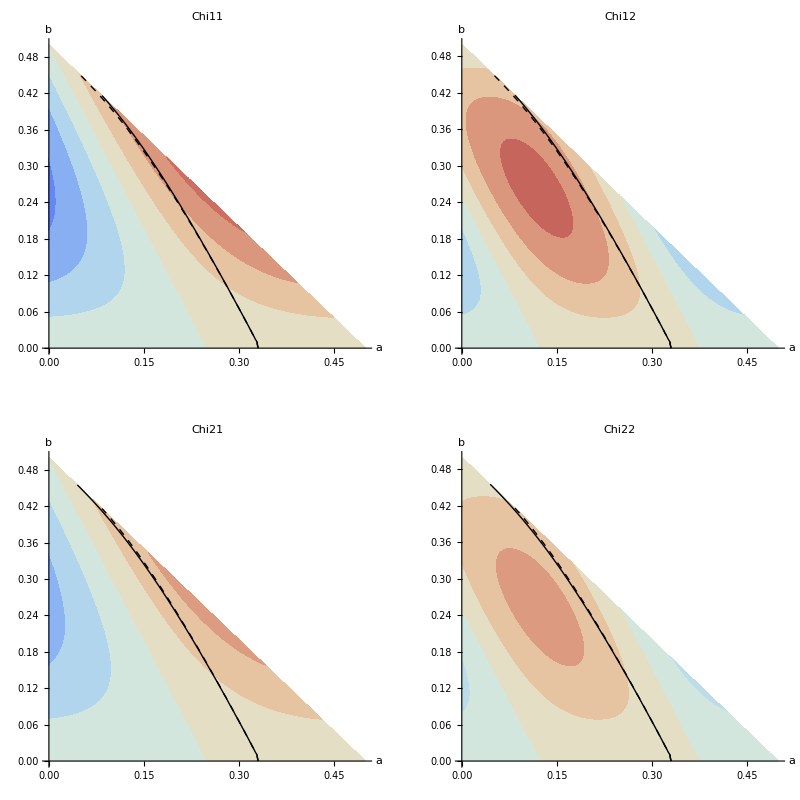

```mathematica
s1 = PlotFunc[Chi11, Chi12, Chi21, Chi22];
s2 = PlotFunc[Chi12, Chi11, Chi21, Chi22];
s3 = PlotFunc[Chi21, Chi22, Chi11, Chi12];
s4 = PlotFunc[Chi22, Chi21, Chi11, Chi12];
GraphicsGrid[{{s1, s2},{s3, s4}}]
```

```mathematica
BarLegend[{"ThermometerColors",{-0.5,0.5}}, 10]
```